## Multivariable Differentiation Lab Define the function T:

```mathematica
T[t_,x_] = Subscript[T, 0]+Subscript[T, 1]*ⅇ^(-λ*x)*Sin[ω*t-λ*x];
```

### Find dT/dt:

```mathematica
D[T[t,x], t]
```

```mathematica
ⅇ^(-x λ) ω Cos[x λ-t ω] Subscript[T, 1]
```

The importance of dT/dt is being able to find the change in Frost Penetration with respect to a changing time, t variable at a constant depth, x.

### Find dT/dx:

```mathematica
D[T[t,x], x]
```

```mathematica
-ⅇ^(-x λ) λ Cos[x λ-t ω] Subscript[T, 1]+ⅇ^(-x λ) λ Sin[x λ-t ω] Subscript[T, 1]
```

The importance of dT/dx is being able to find the change in Frost Penetration across multiple depths, x, given a static time, t.

### Graph T[t,x]

```mathematica
λ=0.2;
ω=2π/365;
Subscript[T, 0]=0;
Subscript[T, 1]=10;
point = T [83.8235, 0];
Show[Plot3D[T[t,x],{t,0,300},{x,0,15},PlotLabel->"Frost Penetration",AxesLabel->{"t (days)", "x (feet)","Temp (degrees)"} ,PlotLegends->{T"(83.8235,0)"}, Axes->True], Graphics3D[Point[{83.825, 0, point}],PointSize[0.2],PlotStyle->Red]]
```

-Graphics3D-

### Given Starting Points P1, P2, Find: etc...

```mathematica
P1x=119.118;
P1y=1.98529;
P2x=83.8235;
P2y=0;
```

### Find the gradient of function T(t,x)

```mathematica
grad[t_,x_]={D[T[t,x], t],D[T[t,x], x]}
```

{4/73 ⅇ^(-0.2 x) π Cos[(2 π t)/365-0.2 x],-2. ⅇ^(-0.2 x) Cos[(2 π t)/365-0.2 x]-2. ⅇ^(-0.2 x) Sin[(2 π t)/365-0.2 x]}

### Determine the direct of the gradient evaluated at the point P1

```mathematica
grad[t_,x_]={D[T[t,x], t],D[T[t,x], x]};
grad[P1]
```

```mathematica
grad[119.118,1.98529]
```

{-0.00955624,-1.22897}

### Create vector v between points P1 and P2

```mathematica
V={P2x-P1x,P2y-P1y}
```

{-35.2945,-1.98529}

### Compute the Unit Vector U from vector V

```mathematica
U=V/Norm[V]
```

{-0.998422,-0.0561605}

### Calculate the directional derivative at point P1 in the direction U

```mathematica
Duf1[t_,x_]=Dot[{D[T[t,x], t],D[T[t,x], x]},U];
Duf1[P1x,P1y]
```

0.0785608

## Visualize the Surface T(t,x) using a contour plot

### Create a contour plot of the function T(t,x) using the ContourPlot Command for the domains given.

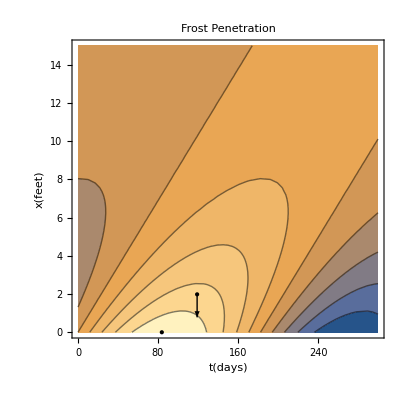

```mathematica
Show[ContourPlot[T[t,x],{t,0,300},{x,0,15},PlotLabel->"Frost Penetration",FrameLabel->{"t(days)","x(feet)"},Axes->True],Graphics[Point[{P1x,P1y}],PointSize[.02],Red],Graphics[Point[{P2x,P2y}],PointSize[.02],Red],Graphics[Arrow[{{P1x,P1y},{P1x,.78239}}]]]
```

NOTE: I am not sure how to make Red work, I have tried PlotStyle and just the Red commands but they refuse to turn red.